### Experimenting v1

```mathematica
ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}, {{50, 5}, {52,3}}, "Body"->True]
```

```mathematica
PlotCA[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}, {{50, 5}, {52,3}}, "Body"->True]]
```

```mathematica
Table[SeedRandom[4444 + i] ; PlotCA[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}]], {i, 50}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Position[, -Graphics-]
```

{{29}}

```mathematica
SeedRandom[4444 + 29];PlotCA[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}, <|{52,203}->0, {95, 210}->"Random"|>]]
```

-Graphics-

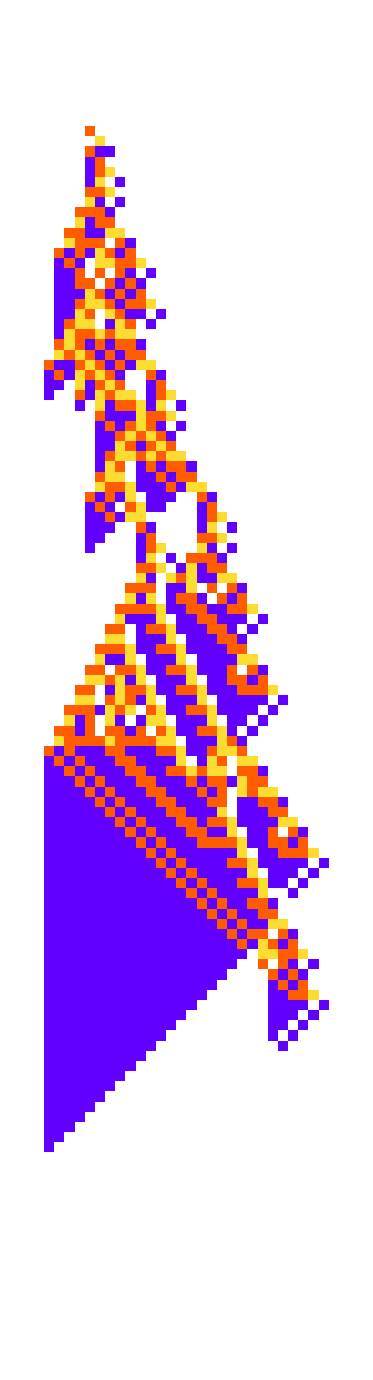

```mathematica
PlotCA[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{110, {-200, 200}}, {}]]
```

```mathematica
SeedRandom[4444 + 29];PlotCA[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}, <|{52,203}->0, {86, 218}->0,{87, 218}->2 |>], Frame->True, FrameTicks->All, Mesh->True]
```

-Graphics-

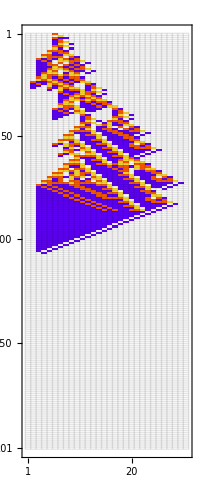

```mathematica
SeedRandom[4444 + 29];PlotCA[First[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}, <|{52,203}->0 , {86, DeleteCases[Range[200, 219], 218]}->2, {86, 218}->0|>]], Frame->True, FrameTicks->All, Mesh->True]
```

```mathematica
SeedRandom[4444 + 29];PlotCA[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}, <|{52,203}->0 , |>], Frame->True, FrameTicks->All, Mesh->True]
```

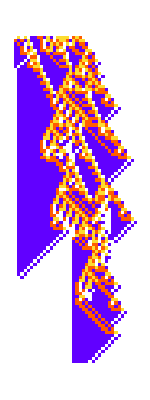

```mathematica
PlotCA[CellularAutomaton[{299459058088077823758143088095350287424,4,1}, {RandomChoice[{0, 1, 2, 3}, 20], 0}, 100]]
```

### Outtakes

So most of aren’t able to achieve their goal, if we do two perturbations:

```mathematica
Append[#, First[Keys[#]] + RandomChoice[{-2, -1, 1, 2}, 2]-> "Random"]&[RandomChoice[allperts[k4reg[[19, 1]], {{1}, 0},{200, {-200, 200}}]] ]
```

<|{64,216}→3,{65,214}→Random|>

```mathematica
GraphicsRow[Table[PlotCA[[k4reg[[19, 1]], {{1}, 0}, {200, {-200, 200}}, 3]], 10]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
SeedRandom[5570];With[{aps = allperts[k4reg[[19, 1]], {{1}, 0},{500, {-200, 200}}]},GraphicsRow[Table[PlotCA[[k4reg[[19, 1]], {{1}, 0}, {200, {-200, 200}}, Append[#, First[Keys[#]] + RandomChoice[{-2, 2}, 2]-> "Random"]&[RandomChoice[aps] ]], "ArrowSize"->Small, "Graphics"->{Haloing[Lighter[Cyan, .85], .01]}], 10]]]
```

-Graphics-

```mathematica
GraphicsRow[Table[PlotCA[[k4reg[[19, 1]], {{1}, 0}, {500, {-200, 200}}]], 10]]
```

-Graphics-

Looking at the widths, many of the automaton seem to have a growth phase and a death phase. To prove this, we can look at the “growth curves” of a bunch of the automaton, by simply taking the width at each step:

And we can compare that with just a random sample of programs:

So clearly, because of our fitness function we are getting a commonality between the shapes of automaton. But are there any low-level mechanisms that we can measure that are more common in the evolved automaton than in the regular? For example, we can look at just the number of white squared outputs, in random programs vs. our evolved ones.

### Draft v1

So one of the critical recent claims made by Stephen Wolfram and us at the Wolfram Institute is that adaptive systems work by putting pieces of irreducible computation together to achieve some goal. And the implication is that the way these adaptive systems work is hard and in some cases impossible to understand. To get a sense for this, here are some cellular automata that we have evolved to maximize their finite length:

```mathematica
k4reg= Select[,Last[#]>100&];
```

```mathematica
GraphicsGrid[Partition[PlotCA/@k4reg[[;;20, 1]], 10]]
```

-Graphics-

And the key point is that the subpatterns within each automaton are so complex that it’s not clear why any of these end up “terminating” and therefore achieving their goal.  To convince ourselves of this, we can look at what happens if we change one single cell in the pattern.

```mathematica
GraphicsRow[Table[PlotCA[[k4reg[[19, 1]], {{1}, 0}, {200, {-200, 200}}]], 10]]
```

-Graphics-

So most of them failed to terminate given just a single bit change. One question you may have is, how similar is this model to what actual organisms do? Are biological processes really full of irreducibility? One test we can do is just to observe embryogenesis, say in a mouse:

(phillip keller, mcdale et all Cell https://www.youtube.com/watch?v=R2I4c6C9Ths&t=2232s)

So in this video each color corresponds to a different type of tissue. The orange and blue correspond to the lateral plate mesoderm. The pink and yellow are the somitic mesoderm, the purple is the heart field (cardiogenic mesoderm). The green is the neural tube and the red is the notochord. The categories were identified by looking at the last frame in the imaging data, at which point the cells are anatomically differentiated and can be identified, and then following each cell back from that point to see where it started.

What’s interesting here is that each cell seems to be following a

Okay so there’s a lot to take in here. We see the colors start in a condense and simplified version of the end state. From there, the cells are following rules for their movement and division

```mathematica
SeedRandom[4444 + 29];PlotCA[First[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077823758143088095350287424,4,1},{{1},0},{200, {-200, 200}}, <|{52,203}->0 , {86, DeleteCases[Range[200, 219], 218]}->2, {86, 218}->0|>]], Frame->True, FrameTicks->All, Mesh->True]
```

-Graphics-

### A better model for biological processes

What is the nature of biological processes. How do they look? What can they achieve? What happens when they go wrong?  These are such simple questions, and yet the field of biology, in my view, has largely failed to give people good answers.

In my experience, modern academic institutions are really bad at answering big questions like this, and most of the best “scientists” of our time have found ways to do science not because of these institutions but despite them.

So okay these are bold statements, who do I think I am, right? Well, I think most biologists have largely missed the powerful new paradigm of using computation as opposed to mathematics for their models. And because of this, they have been limited in their ability to give a good high-level description of what is going on in biology. Stephen Wolfram has recently pioneered some groundbreaking computational models for biology. Starting as a fan of the research, and eventually becoming a collaborator, I’ve become convinced that we’ve struck gold and that with these models, we’re now in a position to understand the high-level features of biology better than anyone ever has before.

Again, big statements. So what are our models and what claims can we make from them?

We use cellular automaton as a model organism, making single bit changes to the ruleset and keeping the changes that give a larger or equal finite length.

And the similarities are already striking between this and real evolution. At a high level, we have discrete branches of patterns, corresponding to branches in the tree of life.

We also have sharp increases in “fitness” quickly followed by the plateauing stage, within our evolutions.

Looking more closely at the specific patterns, we have these subpatterns that work together to achieve a particular goal. And the implication is that adaptive processes like evolution are “mining irreducibility” to achieve their goal.

In other words, with each improvement step, they’re finding irreducible subprograms that increase their finite length. And as a result, it’s clear that certain parts of our organism are just completely unexplainable, and trying to come up with a reason for why they exist, is like trying to jump ahead of an irreducible process.

But just how much reducibility and irreducibility are in these patterns. Given the fact that we are selecting for a particular feature (finite length), you’d expect that there is at least some commonalities between the organisms.

To get at this, we can look at an adaptively evolved set of organisms:

And compare that to a random sample of our rule space:

And from this, we can see that the main problem that adaptive evolution is solving in this case is growth inhibition. And because of that, our evolved organisms exhibit much more of a “worm-like” shape then the random group.

So this is a high-level pocket of reducibility, and if a biologist were looking at this, he could indeed form some theory about the shape of organisms. But what about more low-level mechanisms, like say the different rule frequencies of the random group and the adaptive group:

So each bar corresponds to the number of automaton in the group that had that rule.

And here is data from 10 random groups:

So clearly, there is some statistically significant difference here. And based on our conclusion that the evolved automata are better at growth inhibition, we can look at “edge-rules” or rules with two white squares. These rules, highlighted here, are critical for growth inhibition and we’d expect the adapted group to have far more white square outputs for these rules.

Looking at the frequencies of the “growth-inhibiting” rules we can see that they are indeed “active” much more frequently in the adaptive group. So this would correspond to a low-level theory that we could form about our organisms, similar to how a molecular biologists could find certain genes and proteins that are associated with certain behaviors. But the key point, is that only some of these rules in our automata actually have a “function” that you can map to the behavior. For many of the “inner-rules” their use isn’t so clear.

And the reason is because our fitness-function is not acting heavily on the inner rules. In other words, there are many different ways to grow, and so the ones evolution finds are not necessarily explainable. But you may be wondering, can we make our fitness function more restrictive, and force the irreducibility out of the system?

Well, one common theme in biology is dealing with noise in the environment, and still being able to function. So we can do our same evolution, but make perturbations to the automaton as it grows, and take the minimum length from all the perturbed automaton. Then, we try to increase that minimum length.

And the results are very nice. Because what we get are far “simpler” organisms that use more explainable mechanisms.

So the solution that is often found is to have some pattern that ends despite, many of the details of the internal subpatterns:

And what we’ve touched on here is an important law of biology an adaptive systems, which is the more noise in the environment the more simple and explainable the underlying mechanisms end up being. As an example, animals like frogs, who are hatched from eggs in the wild, we would expect to have far more explainable mechanisms for how their morphogenesis works. But mammals who are grown mostly from the safety of the womb, wouldn’t have to deal with as much noise. So, I suspect that the embryogenesis process, especially the early stage, is far more irreducible and specific then something like a frog. And therefore if you mix up a human embryo, you’d get a completely different structure, as opposed to a frog / planeria embryo, who can handle these perturbations.

And in terms of explainability, it is known that planeria use a general sorting network to complete morphogenesis, and so you can perturb the system in the right way and get a two-headed flatworm. This would definitely not be possible I believe in the mammalian case.

So okay, but just how reducible are these highly-robust guys? Well as we can see, they still have pieces of irreducibility and are not perfectly robust. And this is the consequence of the physical limitations of the cellular automaton system here, as well as the limitations of our adaptive search.

And because of this, if we take these guys outside of their noise tolerance level, outside of their evolved track, what we get is irreducible behavior. And the fundamental problem of medicine is then trying to get these guys back on track.

And so what has happened in most diseases, is something has happened to the evolved guard rails of irreducibility. But the implication is that quite often you can steal ideas from biology, and just apply them in a new way:

But even this still has irreducibility in it, and is computationally and therefore economically expensive.

We should pause here to look at some actual medicine data. And what we see is that actually most of the diseases are self-inflicted! And then we spend all this computational effort to try to pick up the pieces. So our model would suggest that we should focus on simply not throwing ourselves off the cliffs of irreducibility.

What we’re doing is the equivalent of the following: We have an evolved track that we can walk down the mountain. But instead we just jump off the cliff and then spend a bunch of money and time trying to building parachutes as we fall down.

So we’ve mostly talked about avoidance of diseases, but what about increased performance. How can we get these automaton to do their job even better?

Similar story of computational irreducibility, there are some shortcuts, but still computationally expensive

Especially if goals are different than evolved, we’d suspect quite a lot of low-hanging fruit. New goals == low-hanging fruit

#### Give up as often as possible

Terminal units are quite invariant. Any chance to improve them is critical. We should try for humanoid robots.

So one trick that can be used is to steal the

And these systems, are very good models of highly-adapted organisms like humans. They tried to squeeze the irreducibility out of their system,

[[Maybe dive into healing cancer using this mechanism]]

### Roadmap

Talk about primitive organisms. mining irreducibility to approximate some behavior.
Discrete branches of life. Simple programs and hill climbing. 
The example of branching networks. 
Talk about mature organisms. 
Learning how to be robust. 
Comparison with embryogenesis. 
Sorting algorithms. 
What happens when you take these guys out of their evolved state. 
The problem of medicine. 
Congenital heart disease data. 
Understanding the organism. 
Using already evolved mechanisms.   
The deeper problem of medicine. 
The other end of the spectrum? 
Does biology matter.

### Does biology matter?

Maybe not. Maybe the future will be silicon, not carbon, who knows. But if not, then we can be sure that humans are the future. To understand biology is to understand humans.

When you ask what is the determinant of the future of our world. It’s us. It’s not bears, it’s not tigers it’s not trees, it’s not bacteria. We are the only ones with the power to steer the world in a particular direction.

So I would argue that the ultimate goal of biology should be to help humans do what they do better.

So let’s take a survey of the human landscape, and try to see, what is holding us back? One angle, is to look at what kills us. Obviously, if you are dead, you can’t contribute.

Now here comes the surprising part. When people think medicine, they mostly think drugs, a doctor in a lab coat coming to tell you bad news from a specific test.

But in reality, the vast majority of human disease is self-inflicted: drugs, poor diet, lack of exercise, bad habits. (Tell mom MSQ stories).

So basically, what is happening is we are creating these self-inflicted perturbation, taking our systems off the track that they evolved to deal with, and then we ask doctors to try to pick up the pieces.

And it’s quite obvious to many people, (this is not a new nor my idea) that instead of doing this we should be